```mathematica
(* BS functions *)
```

```mathematica
NCDF[x_] := 1/2(1+Erf[x/Sqrt[2]])
```

```mathematica
CBS[x_,v_] := NCDF[1/v(-x)+1/2 v]-Exp[x] NCDF[1/v(-x)-1/2v]
```

```mathematica
sigimp[x_,c_] := v/.FindRoot[CBS[x,v]==c,{v,0.1}]
```

```mathematica
CBS[0.1,0.1]
```

0.00875177

```mathematica
sigimp[0.1,0.00875177]
```

0.1

```mathematica
Afwd[S0_,rho_] := S0 (Exp[rho]-1)/rho
```

```mathematica
DiscF[rho_] := Exp[-rho]
```

```mathematica
xlogstrike[k_,r_,t_] := Log[k r t/(Exp[r t]-1)]
```

```mathematica
(* Leading order Asian implied variance *)
```

```mathematica
SigA0Sq[x_] := 1/3(1 + 1/5 x - 1/84 x^2 - 17/10500 x^3+8959/16170000x^4)
```

```mathematica
(* Second order corrections: ATM, the linear (skew) and quadratic (convexity) terms *)
```

```mathematica
(* SigA2ATM[sig_,r_,t_] := sig^2 (1/3 - 61/9450 sig^2 t + 1/12 r t) *)
```

```mathematica
SigA2[k_,sig_,r_,t_] := sig^2 SigA0Sq[xlogstrike[k,r,t]]+sig^2 ( - 61/9450 sig^2 t + 1/12 r t)
```

```mathematica
SigA2lin[k_,sig_,r_,t_] := sig^2 ( -34/23625 sig^2 t )xlogstrike[k,r,t]
```

```mathematica
SigA2quad[k_,sig_,r_,t_] := sig^2 ( 1657/4158000sig^2 t-5/2016 r t )xlogstrike[k,r,t]^2
```

```mathematica
(* The 7 cases of Linetsky *)
```

```mathematica
(* Case 1 *)
```

```mathematica
xlogstrike[1,0.02,1]
```

-0.0100167

```mathematica
SigA1exact=sigimp[xlogstrike[1,0.02,1],0.055986/(DiscF[0.02] Afwd[2,0.02])]
```

0.057816

```mathematica
(* Predicted Asian impvol keeping the subleading order correction *)
```

```mathematica
Sqrt[SigA2[1,0.1,0.02,1]]
```

0.0578159

```mathematica
Sqrt[SigA2[1,0.1,0.02,1]+SigA2lin[1,0.1,0.02,1]]
```

0.0578159

```mathematica
Sqrt[SigA2[1,0.1,0.02,1]+SigA2lin[1,0.1,0.02,1]+SigA2quad[1,0.1,0.02,1]]
```

0.0578159

```mathematica
(* Predicted Asian option price *)
```

```mathematica
DiscF[0.02] Afwd[2,0.02] CBS[Log[2.0/Afwd[2,0.02]],Sqrt[SigA2[1,0.1,0.02,1]]]
```

0.0559859

```mathematica
DiscF[0.02] Afwd[2,0.02] CBS[Log[2.0/Afwd[2,0.02]],Sqrt[SigA2[1,0.1,0.02,1]+SigA2lin[1,0.1,0.02,1]]]
```

0.0559859

```mathematica
DiscF[0.02] Afwd[2,0.02] CBS[Log[2.0/Afwd[2,0.02]],Sqrt[SigA2[1,0.1,0.02,1]+SigA2lin[1,0.1,0.02,1]+SigA2quad[1,0.1,0.02,1]]]
```

0.0559859

```mathematica
Afwd[2,0.02]/2
```

1.01007

```mathematica
(* Plot the Asian implied volatility vs K/S0 *)
```

```mathematica
case1ATM = {{1,5.7816}}
```

{{1,5.7816}}

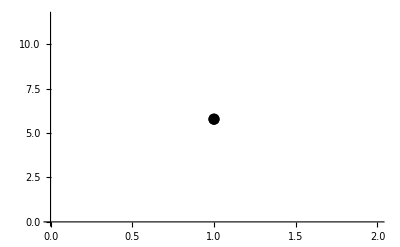

```mathematica
p1dot=ListPlot[case1ATM,PlotStyle->{ Black,PointSize[0.02]}]
```

```mathematica
l1=Line[{{Afwd[2,0.02]/2,5.3},{Afwd[2,0.02]/2,6.0}}];
```

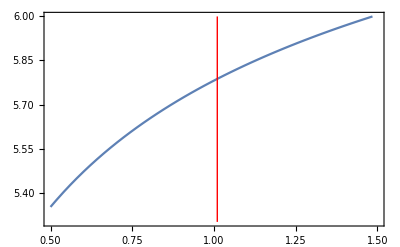

```mathematica
p1ATM=Plot[100 Sqrt[SigA2[k,0.1,0.02,1]],{k,0.5,1.5}, PlotRange -> {{0.5,1.5},{5.3,6}}, Frame -> True,Epilog->{Red,l1}]
```

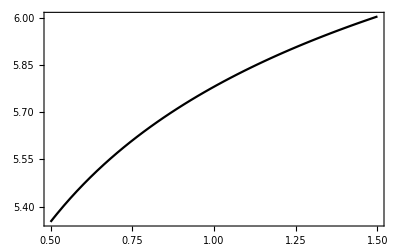

```mathematica
p1lin=Plot[100 Sqrt[SigA2[k,0.1,0.02,1]+SigA2lin[k,0.1,0.02,1]], {k,0.5,1.5},PlotStyle-> {Black}, Frame -> True]
```

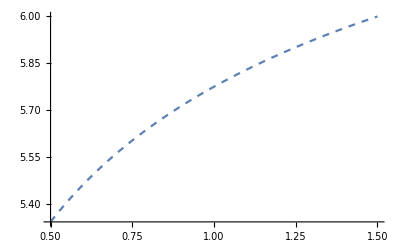

```mathematica
p1LO=Plot[100 0.1Sqrt[SigA0Sq[Log[k]]],{k,0.5,1.5},PlotStyle-> Dashed]
```

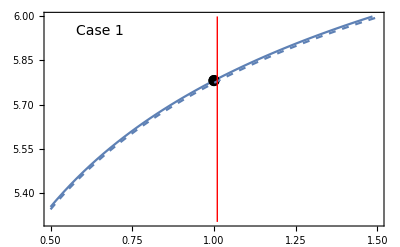

```mathematica
Show[p1ATM,p1dot, p1LO,Epilog-> {Text[Style["Case 1",FontSize-> 14], {0.65,5.95}],{Red,l1}}]
```

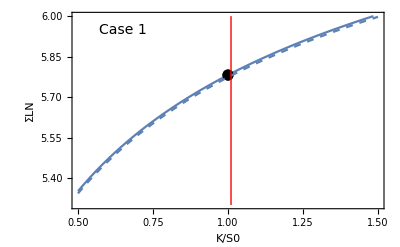

```mathematica
Show[%,FrameLabel->{{HoldForm[ΣLN],None},{HoldForm[K/S0],None}}]
```

```mathematica
(* Case 2 *)
```

```mathematica
Log[2.0/Afwd[2,0.18]]
```

-0.0913496

```mathematica
DiscF[0.18] Afwd[2,0.18] CBS[Log[2.0/Afwd[2,0.18]],Sqrt[SigA2[1,0.3,0.18,1]]]
```

0.218362

```mathematica
DiscF[0.18] Afwd[2,0.18] CBS[Log[2.0/Afwd[2,0.18]],Sqrt[SigA2[1,0.3,0.18,1]+SigA2lin[1,0.3,0.18,1]]]
```

0.218364

```mathematica
DiscF[0.18] Afwd[2,0.18] CBS[Log[2.0/Afwd[2,0.18]],Sqrt[SigA2[1,0.3,0.18,1]+SigA2lin[1,0.3,0.18,1]+SigA2quad[1,0.3,0.18,1]]]
```

0.218363

```mathematica
sigimp[xlogstrike[1,0.18,1],0.218387/(DiscF[0.18] Afwd[2,0.18])]
```

0.175389

```mathematica
case2ATM = {{1,17.5389}}
```

{{1,17.5389}}

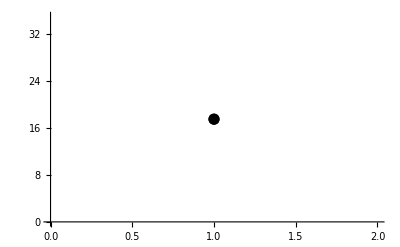

```mathematica
p2dot=ListPlot[case2ATM,PlotStyle->{ Black,PointSize[0.02]}]
```

```mathematica
l2=Line[{{Afwd[2,0.18]/2,16},{Afwd[2,0.18]/2,18.5}}];
```

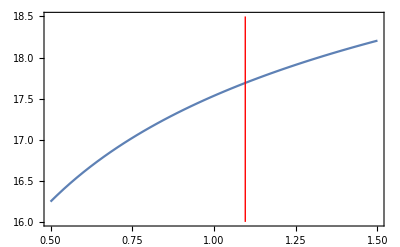

```mathematica
p2ATM=Plot[100 Sqrt[SigA2[k,0.3,0.18,1]],{k,0.5,1.5}, PlotRange -> {{0.5,1.5},{16,18.5}}, Frame -> True, Epilog -> {Red,l2}]
```

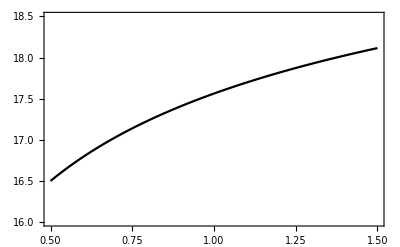

```mathematica
p2lin=Plot[100 Sqrt[SigA2[k,0.3,0.18,1]+SigA2lin[k,0.3,0.18,1]],{k,0.5,1.5}, PlotRange -> {{0.5,1.5},{16,18.5}}, Frame -> True, PlotStyle -> Black]
```

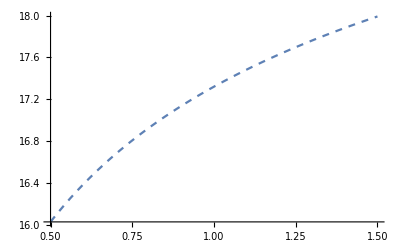

```mathematica
p2LO=Plot[30Sqrt[SigA0Sq[Log[k]]],{k,0.5,1.5},PlotStyle-> Dashed]
```

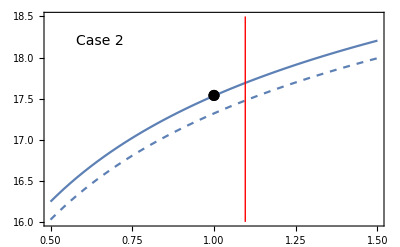

```mathematica
Show[p2ATM,p2LO,p2dot,Epilog-> {Text[Style["Case 2",FontSize-> 14], {0.65,18.2}],{Red,l2}}]
```

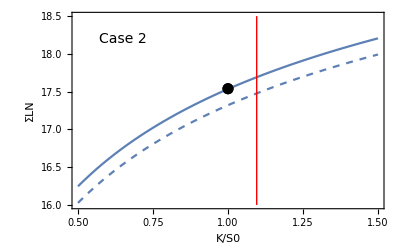

```mathematica
Show[%,FrameLabel->{{HoldForm[ΣLN],None},{HoldForm[K/S0],None}}]
```

```mathematica
(* Case 3 *)
```

```mathematica
DiscF[0.0125 2] Afwd[2,0.0125 2] CBS[xlogstrike[1,0.0125,2],Sqrt[SigA2[1,0.25,0.0125,2]]Sqrt[2]]
```

0.172268

```mathematica
DiscF[0.0125 2] Afwd[2,0.0125 2] CBS[xlogstrike[1,0.0125,2],Sqrt[SigA2[1,0.25,0.0125,2]+SigA2lin[1,0.25,0.0125,2]]Sqrt[2]]
```

0.172269

```mathematica
DiscF[0.0125 2] Afwd[2,0.0125 2] CBS[xlogstrike[1,0.0125,2],Sqrt[SigA2[1,0.25,0.0125,2]+SigA2lin[1,0.25,0.0125,2]+SigA2quad[1,0.25,0.0125,2]]Sqrt[2]]
```

0.172269

```mathematica
xlogstrike[1,0.0125,2]
```

-0.012526

```mathematica
sigimp[xlogstrike[1,0.0125,2],0.172269/(DiscF[0.025] Afwd[2,0.025])]/Sqrt[2]
```

0.144434

```mathematica
case3ATM = {{1,14.4434}}
```

{{1,14.4434}}

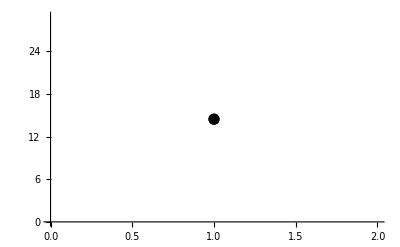

```mathematica
p3dot=ListPlot[case3ATM,PlotStyle->{ Black,PointSize[0.02]}]
```

```mathematica
l3=Line[{{Afwd[2,0.025]/2,13},{Afwd[2,0.025]/2,15}}];
```

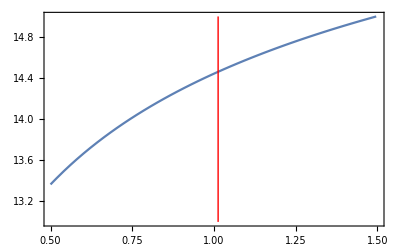

```mathematica
p3ATM=Plot[100 Sqrt[SigA2[k,0.25,0.0125,2]],{k,0.5,1.5}, PlotRange -> {{0.5,1.5},{13,15}}, Frame -> True, Epilog -> {Red,l3}]
```

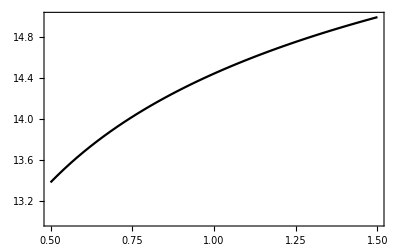

```mathematica
p3lin=Plot[100 Sqrt[SigA2[k,0.25,0.0125,2]+SigA2lin[k,0.25,0.0125,2]],{k,0.5,1.5}, PlotRange -> {{0.5,1.5},{13,15}}, Frame -> True, PlotStyle-> Black]
```

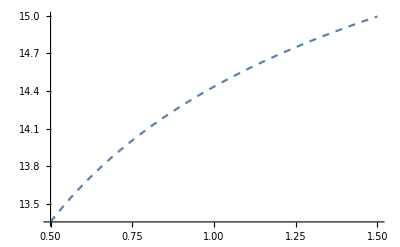

```mathematica
p3LO=Plot[25Sqrt[SigA0Sq[Log[k]]],{k,0.5,1.5},PlotStyle-> Dashed]
```

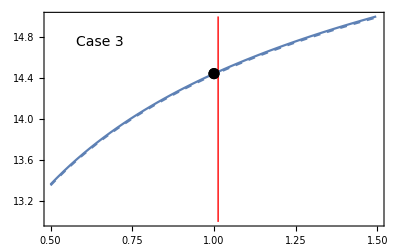

```mathematica
Show[p3ATM,p3LO,p3dot,Epilog-> {Text[Style["Case 3",FontSize-> 14], {0.65,14.75}],{Red,l3}}]
```

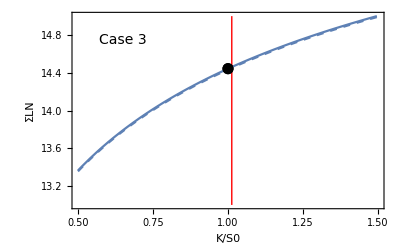

```mathematica
Show[%,FrameLabel->{{HoldForm[ΣLN],None},{HoldForm[K/S0],None}}]
```

```mathematica
(* Case 4 *)
```

```mathematica
xlogstrike[2/1.9,0.05,1]
```

0.0261891

```mathematica
sigimp[xlogstrike[2/1.9,0.05,1],0.193174/(DiscF[0.05] Afwd[1.9,0.05])]
```

0.290526

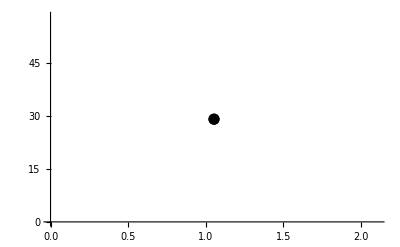

```mathematica
p4dot=ListPlot[{{2/1.9,29.0526}},PlotStyle->{ Black,PointSize[0.02]}]
```

```mathematica
l4=Line[{{Afwd[1.9,0.05]/1.9,27},{Afwd[1.9,0.05]/1.9,30}}];
```

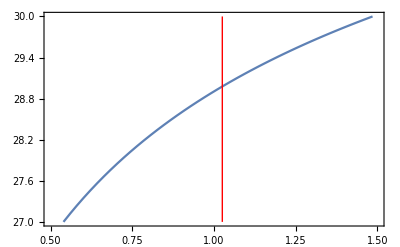

```mathematica
p4ATM=Plot[100 Sqrt[SigA2[k,0.5,0.05,1]],{k,0.5,1.5}, PlotRange -> {{0.5,1.5},{27,30}}, Frame -> True,Epilog-> {Red,l4}]
```

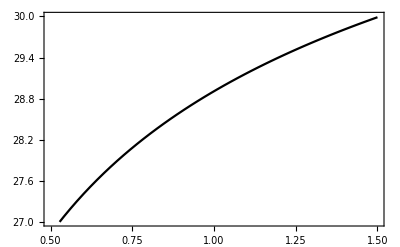

```mathematica
p4lin=Plot[100 Sqrt[SigA2[k,0.5,0.05,1]+SigA2lin[k,0.5,0.05,1]],{k,0.5,1.5}, PlotRange -> {{0.5,1.5},{27,30}}, Frame -> True, PlotStyle -> Black]
```

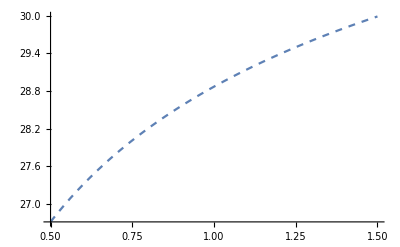

```mathematica
p4LO=Plot[100 0.5Sqrt[SigA0Sq[Log[k]]],{k,0.5,1.5},PlotStyle-> Dashed]
```

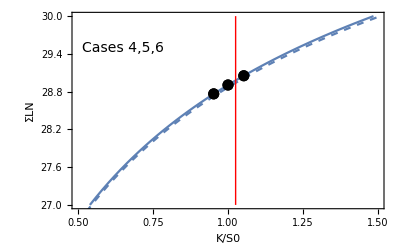

```mathematica
Show[p4ATM, p4LO,p4dot,p5dot,p6dot,Epilog-> {Text[Style["Cases 4,5,6",FontSize-> 14], {0.65,29.5}],{Red,l4}},FrameLabel->{{HoldForm[ΣLN],None},{HoldForm[K/S0],None}}]
```

```mathematica
DiscF[0.05] Afwd[1.9,0.05] CBS[xlogstrike[2.0/1.9,0.05,1],Sqrt[SigA2[2/1.9,0.5,0.05,1]]]
```

0.193176

```mathematica
DiscF[0.05] Afwd[1.9,0.05] CBS[xlogstrike[2.0/1.9,0.05,1],Sqrt[SigA2[2/1.9,0.5,0.05,1]+SigA2lin[2/1.9,0.5,0.05,1]]]
```

0.193173

```mathematica
DiscF[0.05] Afwd[1.9,0.05] CBS[xlogstrike[2.0/1.9,0.05,1],Sqrt[SigA2[2/1.9,0.5,0.05,1]+SigA2lin[2/1.9,0.5,0.05,1]+SigA2quad[2/1.9,0.5,0.05,1]]]
```

0.193173

```mathematica
(* Case 5 *)
```

```mathematica
xlogstrike[1,0.05,1]
```

-0.0251042

```mathematica
sigimp[xlogstrike[1,0.05,1],0.246416/(DiscF[0.05] Afwd[2,0.05])]
```

0.289059

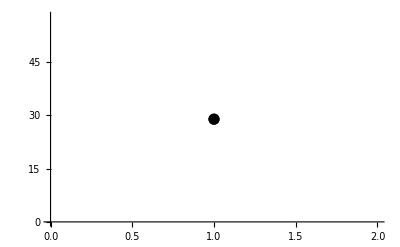

```mathematica
p5dot=ListPlot[{{1,28.9059}},PlotStyle->{ Black,PointSize[0.02]}]
```

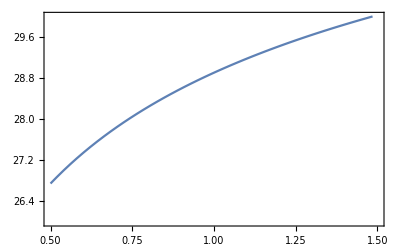

```mathematica
p5ATM=Plot[100 Sqrt[SigA2[k,0.5,0.05,1]],{k,0.5,1.5}, PlotRange -> {{0.5,1.5},{26,30}}, Frame -> True]
```

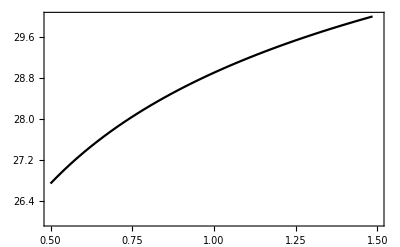

```mathematica
p5lin=Plot[100 Sqrt[SigA2[k,0.5,0.05,1]],{k,0.5,1.5}, PlotRange -> {{0.5,1.5},{26,30}}, Frame -> True, PlotStyle -> Black]
```

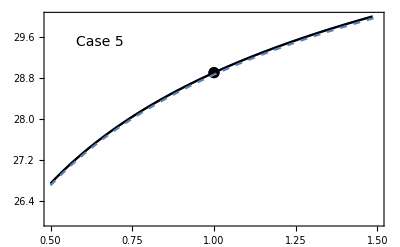

```mathematica
Show[p5ATM,p5lin,p5dot,p4LO,Epilog-> {Text[Style["Case 5",FontSize-> 14], {0.65,29.5}]}]
```

```mathematica
DiscF[0.05] Afwd[2,0.05] CBS[xlogstrike[1.0,0.05,1],Sqrt[SigA2[1,0.5,0.05,1]]]
```

0.246412

```mathematica
DiscF[0.05] Afwd[2,0.05] CBS[xlogstrike[1.0,0.05,1],Sqrt[SigA2[1,0.5,0.05,1]+SigA2lin[1,0.5,0.05,1]]]
```

0.246415

```mathematica
(* Case 6 *)
```

```mathematica
Log[2.0/Afwd[2.1,0.05 ]]
```

-0.0738943

```mathematica
sigimp[xlogstrike[2/2.1,0.05,1],0.306220/(DiscF[0.05] Afwd[2.1,0.05])]
```

0.287648

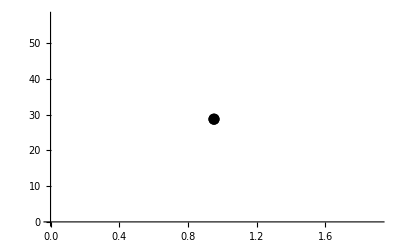

```mathematica
p6dot=ListPlot[{{2/2.1,28.7648}},PlotStyle->{ Black,PointSize[0.02]}]
```

```mathematica
DiscF[0.05] Afwd[2.1,0.05] CBS[xlogstrike[2.0/2.1,0.05,1],Sqrt[SigA2[2.0/2.1,0.5,0.05,1]]]
```

0.306211

```mathematica
DiscF[0.05] Afwd[2.1,0.05] CBS[xlogstrike[2.0/2.1,0.05,1],Sqrt[SigA2[2.0/2.1,0.5,0.05,1]+SigA2lin[2.0/2.1,0.5,0.05,1]]]
```

0.30622

```mathematica
DiscF[0.05] Afwd[2.1,0.05] CBS[Log[2.0/Afwd[2.1,0.05]],Sqrt[SigA2[2.0/2.1,0.5,0.05,1]+SigA2lin[2.0/2.1,0.5,0.05,1]]]
```

0.306269

```mathematica
(* Case 7 *)
```

```mathematica
SigA2ATM[sig_,r_,t_] := sig^2 (1/3 - 61/9450 sig^2 t + 1/12 r t)
```

```mathematica
Log[2.0/Afwd[2,0.05 2]]
```

-0.0504166

```mathematica
sigimp[xlogstrike[1,0.05,2],0.350095/(DiscF[0.1] Afwd[2,0.1])]/Sqrt[2]
```

0.289443

```mathematica
p7dot=ListPlot[{{1,28.9443}},PlotStyle->{ Black,PointSize[0.02]}]
```

-Graphics-

```mathematica
l7=Line[{{Afwd[2,0.05 2]/2,27},{Afwd[2,0.05 2]/2,30}}];
```

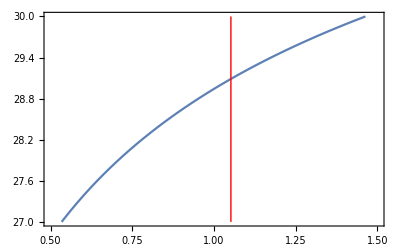

```mathematica
p7ATM=Plot[100 Sqrt[SigA2[k,0.5,0.05,2]],{k,0.5,1.5}, PlotRange -> {{0.5,1.5},{27,30}}, Frame -> True, Epilog -> {Red,l7}]
```

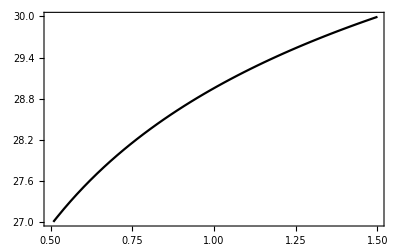

```mathematica
p7lin=Plot[100 Sqrt[SigA2[k,0.5,0.05,2]+SigA2lin[k,0.5,0.05,2]],{k,0.5,1.5}, PlotRange -> {{0.5,1.5},{27,30}}, Frame -> True, PlotStyle -> Black]
```

```mathematica
p7LO=Plot[100 0.5Sqrt[SigA0Sq[Log[k]]],{k,0.5,1.5},PlotStyle-> Dashed]
```

-Graphics-

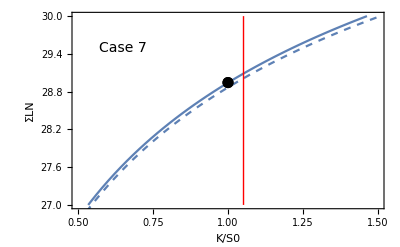

```mathematica
Show[p7ATM,p7LO,p7dot,Epilog-> {Text[Style["Case 7",FontSize-> 14], {0.65,29.5}],{Red,l7}},FrameLabel->{{HoldForm[ΣLN],None},{HoldForm[K/S0],None}}]
```

```mathematica
DiscF[0.05 2] Afwd[2,0.05 2] CBS[Log[2.0/Afwd[2,0.05 2]],Sqrt[SigA2ATM[0.5,0.05,2]]Sqrt[2]]
```

0.351555

```mathematica
DiscF[0.05 2] Afwd[2,0.05 2] CBS[Log[2.0/Afwd[2,0.05 2]],Sqrt[SigA2[1,0.5,0.05,2]]Sqrt[2]]
```

0.350077

```mathematica
DiscF[0.05 2] Afwd[2,0.05 2] CBS[Log[2.0/Afwd[2,0.05 2]],Sqrt[SigA2[1,0.5,0.05,2]]Sqrt[2]+SigA2lin[1,0.5,0.05,2]Sqrt[2]]
```

0.350087

```mathematica
Log[2.0/Afwd[2,0.05 2]]
```

-0.0504166